### Load FeynRules and model

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
CheckHermiticity[LSM+L1Et+L1Jt]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

a$::shdw: 符号 a$ 出现在多个上下文 {FeynRules`,Global`} 中；上下文 FeynRules` 中的定义可能遮蔽或者被其他定义遮蔽.

Merging model-files...

This model implementation was created by

Jing-Hang Fu

Model Version: 1.0

Please cite

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

No vertices found.

0 vertices obtained.

The lagrangian is hermitian.

{}

```mathematica
ComputeWidths[FeynmanRules[L1Et],Save->False];
%[[Position[%[[All,1,1]],Et]//Flatten]];
{%[[All,1]],
(%[[All,2]]*1000//.MEt->2MT//NumericalValue)}//Transpose;
{%[[All,1]],(({%[[All,2]][[1]]*MZ^4/((2MT)^2-MH^2)^2}~Join~%[[All,2]][[2;;-1]])//NumericalValue)*MeV}//MatrixForm//NumberForm[#,{10,3}]&
GammattbWbW=(2*(1.3148+0.027*(MT-172.69))*(1-vv^2/8)//.vv->(gJt^2*64*Pi)^(1/3)//NumericalValue)*GeV;
%%[[2]]/1000/MeV*GeV//Total//NumberForm[#,{10,3}]&
{GammattbWbW,%+GammattbWbW}//NumberForm[#,{10,3}]&
{%%%%[[1]],%%%%[[2]]/1000/%[[2]]*10^4/MeV*GeV}//MatrixForm//NumberForm[#,{10,2}]&
{%%%/%%[[2]],%%[[1]]/%%[[2]]}*10^4//NumberForm[#,{10,2}]&
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

8 possible non-zero vertices have been found -> starting the computation:  / 8.

8 vertices obtained.

Flavor expansion of the vertices:  / 8

Computing the squared matrix elements relevant for the 1->2 decays:

/ 6

({Et,H,Z} | {Et,G,G} | {Et,W^†,W} | {Et,Z,Z} | {Et,A,A} | {Et,A,Z}
5.875 MeV | 16.176 MeV | 1.341 MeV | 0.069 MeV | 0.093 MeV | 0.023 MeV)

0.024 GeV

{2.592 GeV,2.616 GeV}

({Et,H,Z} | {Et,G,G} | {Et,W^†,W} | {Et,Z,Z} | {Et,A,A} | {Et,A,Z}
22.46 | 61.84 | 5.13 | 0.26 | 0.36 | 0.09)

{90.14,9909.86}

```mathematica
ComputeWidths[FeynmanRules[L1Jt],Save->False];
%[[Position[%[[All,1,1]],Jt]//Flatten]];
{%[[All,1]],(%[[All,2]]*1000//.MJt->2MT//NumericalValue)*MeV}//Transpose//MatrixForm//NumberForm[#,{10,3}]&
GammattbWbW=(2*(1.3148+0.027*(MT-172.69))*(1-vv^2/8)//.vv->(gJt^2*64*Pi)^(1/3)//NumericalValue)*GeV;
%%[[All,2]]/1000/MeV*GeV//Total//NumberForm[#,{10,3}]&
{GammattbWbW,%+GammattbWbW}//NumberForm[#,{10,3}]&
{%%%%[[All,1]],%%%%[[All,2]]/1000/%[[2]]*10^4/MeV*GeV}//Transpose//MatrixForm//NumberForm[#,{10,2}]&
{%%%/%%[[2]],%%[[1]]/%%[[2]]}*10^4//NumberForm[#,{10,2}]&
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

16 possible non-zero vertices have been found -> starting the computation:  / 16.

16 vertices obtained.

Flavor expansion of the vertices:  / 16

Computing the squared matrix elements relevant for the 1->2 decays:

/ 16

({Jt,A,H} | 0.628 MeV
{Jt,H,Z} | 0.084 MeV
{Jt,b,b^-} | 4.891 MeV
{Jt,c,c^-} | 0.134 MeV
{Jt,d,d^-} | 0.064 MeV
{Jt,e,e^-} | 0.078 MeV
{Jt,mu,mu^-} | 0.078 MeV
{Jt,s,s^-} | 0.064 MeV
{Jt,ta,ta^-} | 0.078 MeV
{Jt,u,u^-} | 0.134 MeV
{Jt,ve,ve^-} | 0.008 MeV
{Jt,vm,vm^-} | 0.008 MeV
{Jt,vt,vt^-} | 0.008 MeV
{Jt,W^†,W} | 5.720 MeV
{Jt,A,Z} | 0.720 MeV
{Jt,Z,Z} | 0.057 MeV)

0.013 GeV

{2.592 GeV,2.605 GeV}

({Jt,A,H} | 2.41
{Jt,H,Z} | 0.32
{Jt,b,b^-} | 18.78
{Jt,c,c^-} | 0.51
{Jt,d,d^-} | 0.25
{Jt,e,e^-} | 0.30
{Jt,mu,mu^-} | 0.30
{Jt,s,s^-} | 0.25
{Jt,ta,ta^-} | 0.30
{Jt,u,u^-} | 0.51
{Jt,ve,ve^-} | 0.03
{Jt,vm,vm^-} | 0.03
{Jt,vt,vt^-} | 0.03
{Jt,W^†,W} | 21.96
{Jt,A,Z} | 2.76
{Jt,Z,Z} | 0.22)

{48.95,9951.05}

```mathematica
{MT,2MT,MJt}//NumericalValue
```

{172.57,345.14,345.14}

### generate FeynArts LO model

```mathematica
Quit
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Jing-Hang Fu

Model Version: 1.0

Please cite

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
FeynmanGauge = True;
WriteFeynArtsOutput[L1JtZA,LSM+L1Et+L1Jt-L1JtZA,
Output->NotebookDirectory[]<>"FeynArts-3.12/Models/Toponium_LO_FA",
GenericFile->True,FlavorExpand->True]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_LO_FA

CreateDirectory::eexist: D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12\Models\Toponium_LO_FA 已经存在.

Calculating Feynman rules for L1

Calculating Feynman rules for L2

Redefining classes in such a way that each particle is in a separate FeynArts class.

See NewFeynArtsClasses[] for more information on the new classes

Restarting Feynman rule calculation, setting FlavorExpand -> True.

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

Calculating Feynman rules for L2

Starting Feynman rules calculation for L2.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

177 possible non-zero vertices have been found -> starting the computation:  / 177.

162 vertices obtained.

mytimecheck,after LGC

Writing FeynArts model file into directory D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_LO_FA

Writing FeynArts generic file on D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_LO_FA.gen.

### generate LO UFO

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Jing-Hang Fu

Model Version: 1.0

Please cite

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
FeynmanGauge=False;
WriteUFO[LSM+L1Et+L1Jt,Output->"Toponium_LO_UFO"]
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

60 possible non-zero vertices have been found -> starting the computation:  / 60.

55 vertices obtained.

Flavor expansion of the vertices distributed over 16 cores:  / 54

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 58

Squared matrix elent compute in 3.32813 seconds.

/ 68

Decay widths computed in 0.515625 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

Splitting of vertices distributed over 15 kernels.

- Optimizing: /86 .

- Writing files.

Done!

### generate FeynArts QCD-NLO model

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Top 6

Model Version: 1.0

Please cite

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
(*Renormalization and output to FA*)
```

```mathematica
FeynmanGauge = True;
Lren=OnShellRenormalization[LSM+L1Et+L1Jt,QCDOnly->True,Only2Point->False,FlavorMixing->True];
WriteFeynArtsOutput[Lren,
Output->NotebookDirectory[]<>
"FeynArts-3.12/Models/Toponium_QCDNLO_FA",
GenericFile->True]
```

Extracting the mass and kinetic terms to simplify them

Neglecting all terms with more than 2 particles.

renormalizing the fields

All mixing allowed for the renormalization

renormalizing the parameters

Solve::nongen: 可能存在使某些解或所有解都无效的参数值.

renormalizing the masses

renormalizing the other external parameters

Internal parameter renormalization

renormalizing the Lagrangian

with the parameters

paramters before tadpole

with the fields

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_QCDNLO_FA

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

Warning: Class members in the Lagrangian! Not supported by FeynArts.

1 vertex obtained.

Redefining classes in such a way that each particle is in a separate FeynArts class.

See NewFeynArtsClasses[] for more information on the new classes

Restarting Feynman rule calculation, setting FlavorExpand -> True.

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

327 possible non-zero vertices have been found -> starting the computation:  / 327.

300 vertices obtained.

mytimecheck,after LGC

Writing FeynArts model file into directory D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_QCDNLO_FA

Writing FeynArts generic file on D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_QCDNLO_FA.gen.

### NLOCT: Computation of the Counter-terms

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/FeynArts-3.12"];
<< FeynArts`
SetDirectory[NotebookDirectory[]<>"/feynrules-current"];
<< NLOCT`
```

FeynArts 3.12 (24 May 2024)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

- NLOCT -

Version: 1.02

Authors: C. Degrande

Please cite C. Degrande, Comput.Phys.Commun. 197 (2015) 239-262

```mathematica
WriteCT//Options
```

{LabelInternal→True,KeptIndices→{},QCDOnly→False,ZeroMom→{},Assumptions→{},MSbar→False,ComplexMass→False,CTparameters→False,Exclude4ScalarsCT→False,Output→Automatic}

```mathematica
WriteCT["Toponium_FA_QCDNLO",
"Toponium_FA_QCDNLO",
Output->"Toponium_QCDNLO_CT",
QCDOnly->True
]
```

Computing CT for the {S} vertices.

loading generic model file D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12\Models\Toponium_FA_QCDNLO.gen

> $GenericMixing is OFF

generic model {Toponium_FA_QCDNLO} initialized

loading classes model file D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12\Models\Toponium_FA_QCDNLO.mod

> 45 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 160 vertices

> 181 counterterms of order 1

classes model {Toponium_FA_QCDNLO} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 4 Generic, 30 Classes insertions

in total: 4 Generic, 30 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing amplitude finished after 0.1242615

Writing the R2 and UV parts at the class level finished after 0.1242615

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 0.1252669

SU3 algebra finished after 0.1252669

Simplification of the vertices finished after 0.1252669

Vertices {S} finished after 0.1262624

Computing CT for the {F, F} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 2 Generic, 160 Classes insertions

in total: 2 Generic, 160 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 12 Classes amplitudes

in total: 1 Generic, 12 Classes amplitudes

Writing amplitude finished after 0.2953219

Writing the R2 and UV parts at the class level finished after 0.4210320

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes insertions

in total: 1 Generic, 36 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes amplitudes

in total: 1 Generic, 36 Classes amplitudes

Writing the symbolic CT finished after 0.5479657

SU3 algebra finished after 1.2580459

Simplification of the vertices finished after 1.9231286

Vertices {F, F} finished after 1.9231286

Computing CT for the {S, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 22 Classes insertions

> Top. 2: 5 Generic, 101 Classes insertions

in total: 7 Generic, 123 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing amplitude finished after 2.0063193

Writing the R2 and UV parts at the class level finished after 2.0063193

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 2.0093452

SU3 algebra finished after 2.0093452

Simplification of the vertices finished after 2.0093452

Vertices {S, S} finished after 2.0093452

Computing CT for the {V, V} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 23 Classes insertions

> Top. 2: 5 Generic, 216 Classes insertions

in total: 7 Generic, 239 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 3 Generic, 42 Classes amplitudes

in total: 4 Generic, 43 Classes amplitudes

Writing amplitude finished after 2.2186249

Writing the R2 and UV parts at the class level finished after 264.0700428

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

Writing the symbolic CT finished after 264.1190355

SU3 algebra finished after 264.5728126

Simplification of the vertices finished after 264.8940580

Vertices {V, V} finished after 264.8940580

Computing CT for the {F, F, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 1100 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 6 Generic, 1100 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 48 Classes amplitudes

in total: 2 Generic, 48 Classes amplitudes

Writing amplitude finished after 268.7610730

Writing the R2 and UV parts at the class level finished after 268.8841261

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 108 Classes insertions

in total: 1 Generic, 108 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 108 Classes amplitudes

in total: 1 Generic, 108 Classes amplitudes

Writing the symbolic CT finished after 269.1547831

SU3 algebra finished after 270.1754724

Simplification of the vertices finished after 270.9943043

Vertices {F, F, S} finished after 270.9943043

Computing CT for the {F, F, V} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 1564 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 6 Generic, 1564 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 3 Generic, 152 Classes amplitudes

in total: 3 Generic, 152 Classes amplitudes

Writing amplitude finished after 276.5907455

Writing the R2 and UV parts at the class level finished after 278.1764470

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 190 Classes insertions

in total: 1 Generic, 190 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 190 Classes amplitudes

in total: 1 Generic, 190 Classes amplitudes

Writing the symbolic CT finished after 278.7565256

SU3 algebra finished after 280.6323085

Simplification of the vertices finished after 282.5677359

Vertices {F, F, V} finished after 282.5687342

Computing CT for the {V, V, V} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 1922 Classes insertions

> Top. 2: 3 Generic, 68 Classes insertions

> Top. 3: 3 Generic, 68 Classes insertions

> Top. 4: 3 Generic, 68 Classes insertions

in total: 19 Generic, 2126 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 450 Classes amplitudes

> Top. 2: 2 Generic, 2 Classes amplitudes

> Top. 3: 2 Generic, 2 Classes amplitudes

> Top. 4: 2 Generic, 2 Classes amplitudes

in total: 12 Generic, 456 Classes amplitudes

Writing amplitude finished after 285.1844016

Writing the R2 and UV parts at the class level finished after 4188.4362339

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 16 Classes insertions

in total: 1 Generic, 16 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 16 Classes amplitudes

in total: 1 Generic, 16 Classes amplitudes

Writing the symbolic CT finished after 4188.5187856

SU3 algebra finished after 4189.9509576

Simplification of the vertices finished after 4190.5579482

Vertices {V, V, V} finished after 4190.5589469

Computing CT for the {V, V, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 1276 Classes insertions

> Top. 2: 2 Generic, 51 Classes insertions

> Top. 3: 2 Generic, 51 Classes insertions

> Top. 4: 2 Generic, 51 Classes insertions

in total: 16 Generic, 1429 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 185 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

> Top. 3: 1 Generic, 1 Classes amplitudes

> Top. 4: 1 Generic, 1 Classes amplitudes

in total: 5 Generic, 188 Classes amplitudes

Writing amplitude finished after 4192.1396111

Writing the R2 and UV parts at the class level finished after 5313.4219157

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 7 Classes insertions

in total: 1 Generic, 7 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 7 Classes amplitudes

in total: 1 Generic, 7 Classes amplitudes

Writing the symbolic CT finished after 5313.4500180

SU3 algebra finished after 5313.5136085

Simplification of the vertices finished after 5313.6129511

Vertices {V, V, S} finished after 5313.6129511

Computing CT for the {V, S, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 915 Classes insertions

> Top. 2: 2 Generic, 52 Classes insertions

> Top. 3: 2 Generic, 58 Classes insertions

> Top. 4: 2 Generic, 58 Classes insertions

in total: 16 Generic, 1083 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 61 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

> Top. 3: 1 Generic, 1 Classes amplitudes

in total: 4 Generic, 63 Classes amplitudes

Writing amplitude finished after 5314.7373991

Writing the R2 and UV parts at the class level finished after 6287.1331063

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 2 Classes insertions

in total: 1 Generic, 2 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 2 Classes amplitudes

in total: 1 Generic, 2 Classes amplitudes

Writing the symbolic CT finished after 6287.1406175

SU3 algebra finished after 6287.1426168

Simplification of the vertices finished after 6287.1436169

Vertices {V, S, S} finished after 6287.1436169

Computing CT for the {S, S, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 710 Classes insertions

> Top. 2: 2 Generic, 46 Classes insertions

> Top. 3: 2 Generic, 46 Classes insertions

> Top. 4: 2 Generic, 46 Classes insertions

in total: 16 Generic, 848 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing amplitude finished after 6287.9967362

Writing the R2 and UV parts at the class level finished after 6287.9977359

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 6287.9987584

SU3 algebra finished after 6287.9987584

Simplification of the vertices finished after 6287.9997586

Vertices {S, S, S} finished after 6287.9997586

Computing CT for the {V, V, V, V} vertices.

Excluding 19 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 576 Classes insertions

> Top. 2: 2 Generic, 576 Classes insertions

> Top. 3: 2 Generic, 576 Classes insertions

> Top. 4: 2 Generic, 576 Classes insertions

> Top. 5: 2 Generic, 576 Classes insertions

> Top. 6: 2 Generic, 576 Classes insertions

> Top. 7: 4 Generic, 6306 Classes insertions

> Top. 8: 4 Generic, 6306 Classes insertions

> Top. 9: 4 Generic, 6306 Classes insertions

> Top. 10: 3 Generic, 234 Classes insertions

> Top. 11: 3 Generic, 234 Classes insertions

> Top. 12: 3 Generic, 234 Classes insertions

Restoring 19 field point(s)

in total: 33 Generic, 23076 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

> Top. 3: 1 Generic, 1 Classes amplitudes

> Top. 4: 1 Generic, 1 Classes amplitudes

> Top. 5: 1 Generic, 1 Classes amplitudes

> Top. 6: 1 Generic, 1 Classes amplitudes

> Top. 7: 3 Generic, 2363 Classes amplitudes

> Top. 8: 3 Generic, 2363 Classes amplitudes

> Top. 9: 3 Generic, 2363 Classes amplitudes

> Top. 10: 2 Generic, 2 Classes amplitudes

> Top. 11: 2 Generic, 2 Classes amplitudes

> Top. 12: 2 Generic, 2 Classes amplitudes

in total: 21 Generic, 7101 Classes amplitudes

Writing amplitude finished after 6331.1840004

Writing the R2 and UV parts at the class level finished after 10121.3302725

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

Writing the symbolic CT finished after 10121.7274576

SU3 algebra finished after 10142.8533430

Simplification of the vertices finished after 10144.5709351

Vertices {V, V, V, V} finished after 10144.5709351

Computing CT for the {V, V, S, S} vertices.

Excluding 19 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 484 Classes insertions

> Top. 2: 2 Generic, 417 Classes insertions

> Top. 3: 2 Generic, 417 Classes insertions

> Top. 4: 2 Generic, 417 Classes insertions

> Top. 5: 2 Generic, 417 Classes insertions

> Top. 6: 2 Generic, 427 Classes insertions

> Top. 7: 4 Generic, 2628 Classes insertions

> Top. 8: 4 Generic, 2628 Classes insertions

> Top. 9: 4 Generic, 2488 Classes insertions

> Top. 10: 2 Generic, 184 Classes insertions

> Top. 11: 2 Generic, 179 Classes insertions

> Top. 12: 2 Generic, 179 Classes insertions

Restoring 19 field point(s)

in total: 30 Generic, 10865 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 496 Classes amplitudes

> Top. 2: 1 Generic, 496 Classes amplitudes

> Top. 3: 1 Generic, 496 Classes amplitudes

> Top. 4: 1 Generic, 1 Classes amplitudes

> Top. 5: 1 Generic, 1 Classes amplitudes

in total: 5 Generic, 1490 Classes amplitudes

Writing amplitude finished after 10162.3921548

Writing the R2 and UV parts at the class level finished after 10204.5333741

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 10204.5609030

SU3 algebra finished after 10204.6967414

Simplification of the vertices finished after 10204.7180894

Vertices {V, V, S, S} finished after 10204.7180894

Computing CT for the {S, S, S, S} vertices.

Excluding 1 Generic, 10 Classes, and 10 Particles fields

Excluding 19 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 364 Classes insertions

> Top. 2: 2 Generic, 364 Classes insertions

> Top. 3: 2 Generic, 364 Classes insertions

> Top. 4: 2 Generic, 364 Classes insertions

> Top. 5: 2 Generic, 364 Classes insertions

> Top. 6: 2 Generic, 364 Classes insertions

> Top. 7: 3 Generic, 1240 Classes insertions

> Top. 8: 3 Generic, 1240 Classes insertions

> Top. 9: 3 Generic, 1240 Classes insertions

> Top. 10: 2 Generic, 174 Classes insertions

> Top. 11: 2 Generic, 174 Classes insertions

> Top. 12: 2 Generic, 174 Classes insertions

Restoring 1 Generic, 10 Classes, and 10 Particles fields

Restoring 19 field point(s)

in total: 27 Generic, 6426 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing amplitude finished after 10213.4694388

Writing the R2 and UV parts at the class level finished after 10213.4694388

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 10213.4714475

SU3 algebra finished after 10213.4724473

Simplification of the vertices finished after 10213.4724473

Vertices {S, S, S, S} finished after 10213.4724473

before merge 10213.4754467 temp=31.3913192

merging done 10213.5221679

The finite part of those counterterms will be set to zero

{FR$delta[{aS},{}]}

Writing R2 and UV counterterms from Toponium_FA_QCDNLO and Toponium_FA_QCDNLO in Toponium_QCDNLO_CT.nlo

done

{8867.84,Null}

```mathematica
10213.88/60/60 hours
```

2.83719 hours

### generate QCD-NLO UFO

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Top 6

Model Version: 1.0

Please cite

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
Get[$FeynRulesPath<>"/Toponium_QCDNLO_CT.nlo"]
WriteUFO[LSM+L1Et+L1Jt,
UVCounterterms->UV$vertlist//.
Eps[FourVector[-xx__],
FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]]:>-Eps[FourVector[xx],FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]],
R2Vertices->R2$vertlist//.
Eps[FourVector[-xx__],
FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]]:>-Eps[FourVector[xx],FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]],
Output->"Toponium_QCDNLO_UFO"]
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

60 possible non-zero vertices have been found -> starting the computation:  / 60.

55 vertices obtained.

Flavor expansion of the vertices distributed over 16 cores:  / 117

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 59

Squared matrix elent compute in 3.4375 seconds.

/ 68

Decay widths computed in 0.65625 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

Splitting of vertices distributed over 15 kernels.

- Optimizing: /119 .

- Writing files.

Done!

### FeynArts and Feynman Diagram

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/FeynArts-3.12"];
<< FeynArts`
$FAVerbose=0;
```

FeynArts 3.12 (24 May 2024)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

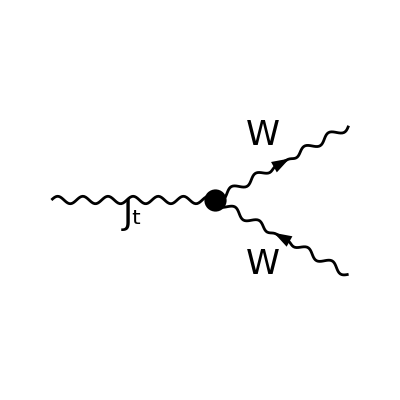

```mathematica
InsertFields[CreateTopologies[0,1->2],
(*{V[5]}->{F[12],-F[12]},*)
{V[5]}->{V[3],-V[3]},
Model->"Toponium_FA_LO",
GenericModel->"Toponium_FA_LO",
InsertionLevel->{Particles}];
Paint[%,Numbering->None,SheetHeader->None,ColumnsXRows->{1,1},ImageSize->{300,300}];
```

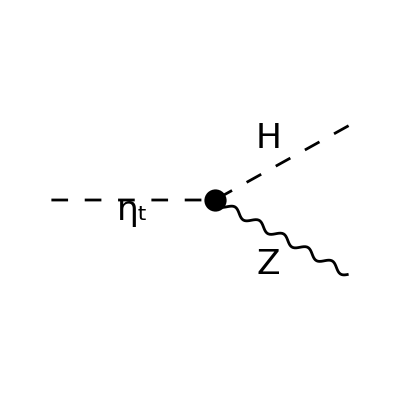

```mathematica
InsertFields[CreateTopologies[0,1->2],
(*{S[4]}->{V[4],V[4]},*)
(*{S[4]}->{V[3],-V[3]},*)
{S[4]}->{S[1],V[2]},
Model->"Toponium_FA_LO",
GenericModel->"Toponium_FA_LO",
InsertionLevel->{Particles}];
Paint[%,Numbering->None,SheetHeader->None,ColumnsXRows->{1,1},ImageSize->{300,300}];
```